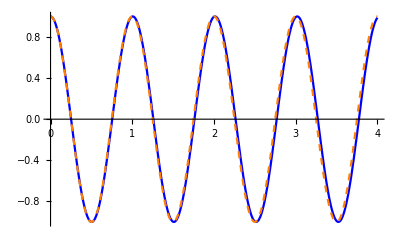

```mathematica
x0=0.1Pi;
dgl1 = {x''[t]+4 Pi^2*Sin [x[t]]==0,x'[0]==0,x[0]==x0}; (*Differentialgleichung mit Randbedingungen*)
sol1=NDSolve[dgl1,x,{t,0,4}]; (*Numerische Lösung der Differentialgleichung*)
plot1=Plot[{ x[t]/x0}/.sol1,{t,0,4},PlotStyle->Blue]; (*Tatsächlicher Verlauf*)
plot2=Plot[{ Cos[2 Pi t]},{t,0,4},PlotStyle->{Orange,Dashed}]; (*Vergleich mit der Näherung*)
Show[plot1,plot2]
```

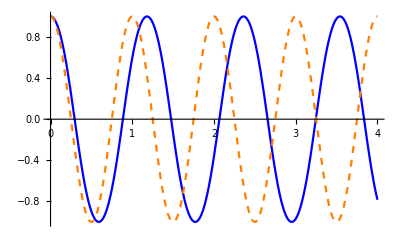

```mathematica
x0=0.5Pi;
dgl2 = {x''[t]+4 Pi^2*Sin [x[t]]==0,x'[0]==0,x[0]==x0};
sol2=NDSolve[dgl2,x,{t,0,4}];
plot1=Plot[{ x[t]/x0}/.sol2,{t,0,4},PlotStyle->Blue];
plot2=Plot[{ Cos[2*Pi t]},{t,0,4},PlotStyle->{Orange,Dashed}];
Show[plot1,plot2]
```

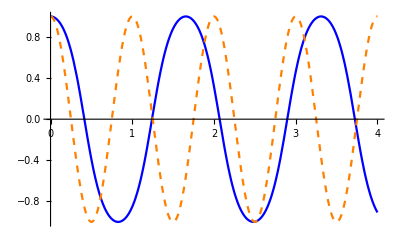

```mathematica
x0=0.8Pi;
dgl3 = {x''[t]+4 Pi^2*Sin [x[t]]==0,x'[0]==0,x[0]==x0};
sol3=NDSolve[dgl3,x,{t,0,4}];
plot1=Plot[{ x[t]/x0}/.sol3,{t,0,4},PlotStyle ->Blue];
plot2=Plot[{ Cos[2Pi t]},{t,0,4},PlotStyle->{Orange,Dashed}];
Show[plot1,plot2]
```

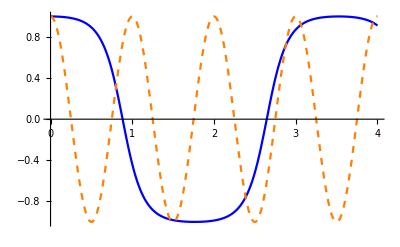

```mathematica
x0=0.99Pi;
dgl4= {x''[t]+4 Pi^2*Sin [x[t]]==0,x'[0]==0,x[0]==x0};
sol4=NDSolve[dgl4,x,{t,0,4}];
plot1=Plot[x[t]/x0/.sol4,{t,0,4},PlotStyle-> {Blue}];
plot2=Plot[{ Cos[2Pi t]},{t,0,4},PlotStyle->{Orange,Dashed}];

Show[plot1,plot2]
```